# QNM Computation and Sequential Storage

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Schwarzschild: vedere dipendenza da infinito al variare dell'ordine dell'espansione. Vedere andamento fissando uno/due parametri. Eventualmente ampliare volume esplorato *)
(* Kerr: vedere che succede con molti punti. Obiettivo futuro: variare spin e quindi qnm *)
(* ECO: per ora in pausa (vedere cosa risultati del resto) *)
```

```mathematica
(* Esplorare Kerr a spin 0 in eps, match e inf così da fare confronto con Schw *)
```

Completati:
1. Segnate funzioni da testare;
2. Sistemato GridSearch/ECO in modo che usi “GridSearchECO” e implementare compatibilità con quanto fatto prima per estendere file esistenti, scegliere direzione percorsa sulla griglia.

Da fare:
3. Testare ottimizzazione anche di derivate successive.

## QNM Finder

We adopt a direct integration method to find the first quasi-normal mode (QNM) of a specific compact object (CO).

First, the perturbation equation is numerically integrated from the horizon (surface in the case of an ECO) to the outside and from infinity to the inside. The two solutions are “attached together” at a point of match. The QNM is estimated as the value smoothing the solution. This is done searching for a continuous derivative, i.e. requesting zero deviation between the left and right side when evaluated at the point of match.

In this Chapter the implementation is generalized to accept any perturbation equation (e.g. Regge-Wheeler or Teukolsky) and boundary condition. Two functions are defined:
	- IntQNM: performs direct integration of the perturbation equation at fixed ω, returns the deviation of the first derivate;
	- FindQNM: searches the root of IntQNM.

```mathematica
(* --- Integrator --- *)
(* NOTE: *)
(* eq_    : perturbation equation - the unknown's name must be ψ *)
(* par_   : list of rules for the CO parameters (e.g. mass, spin, etc.) - names depends on the definition of eq_ *)
(* theta_ : list of rules for the integration parameters (eps, match and inf) *)
(* BCs_   : list of two expressions depending on r and the CO *)
(* In principle par_ and theta_ can be substituted by a single list of rules. 
Although, this distinction allows to more easily separate fixed parameters and variables during a parameter space exploration (see below). 
Here we leave two lists for consistency and to pass them without manipulations of sort *)
IntQNM[ω0_,eq_,par_,theta_,BCs_]:=Module[{rules,param,prec,rI,rM,rE,ξ,ξI,ξE,EQ,BC,b,Δξp},
rules={AccuracyGoal->12,PrecisionGoal->12,WorkingPrecision->20};

(* NOTE: a precision of at least WorkingPrecision is forced across the whole function *)
param=Union[{ω->ω0},par,theta];
prec=Max[20,Precision[param]];param=SetPrecision[param,prec];

rI=2M(1+eps)/.param;
rM=match M/.param;
rE=inf M/.param;

(* The unknown function's name is standardized to ψ *)
EQ=SetPrecision[{eq==0}//.Union[param,{ψ[r]->ξ[r],ψ'[r]->ξ'[r],ψ''[r]->ξ''[r]}],prec];

(* Solution integrating from the horizon *)
BC=SetPrecision[{ξ[rI]==BCs[[1]],ξ'[rI]==D[BCs[[1]],r]}//.Union[{r->rI},param],prec];
ξI=ξ[r]/.NDSolve[Union[EQ,BC],ξ,{r,rI,rM},rules][[1]];

(* Solution integration from infinity *)
BC=SetPrecision[{ξ[rE]==BCs[[2]],ξ'[rE]==D[BCs[[2]],r]}//.Union[{r->rE},param],prec];
ξE=ξ[r]/.NDSolve[Union[EQ,BC],ξ,{r,rE,rM},rules][[1]];

(*Linear combination*)
b=ξI/ξE/.r->rM;(* we fix the coefficients of the linear combination in order for ψn to be continuous at r=rm *)
(*Υn=Piecewise[{{Υhor,r<rm},{b×Υinf,r≥rm}}];*)
Δξp=(D[ξI,r]-D[b ξE,r])/D[ξI,r]/.r->rM;
Return[Δξp];
];
```

```mathematica
(* --- Finder archetype --- *)
(* NOTE: *)
(* ωguess_ : initial guess given to FindRoot *)
(* par_ and theta_ are the same of IntQNM *)
(* EQ and BC are set outside for the specific CO *)
FindQNM[ω0_,par_,theta_]:=Module[{g,ωroot,rules},
rules={AccuracyGoal->6,WorkingPrecision->20};
g[x_?NumericQ]:=IntQNM[x,EQ,par,theta,BC];
ωroot=x/.FindRoot[g[x]==0,{x,ω0},AccuracyGoal->6,WorkingPrecision->20(*,EvaluationMonitor:>Print["ω = ", x," Δψ' = ",Abs[g[x]]]*)][[1]];
Return[{Re[ωroot],Im[ωroot],Abs[g[ωroot]]}];
];
```

## Grid Search

In this Chapter the hyperparameter space is explored along a grid. This approach grants a relatively rigorous search over the selected volume, hence allowing the study of chosen combinations of parameters.

Multiple functions are defined:
	- RunLine: run FindQNM (see previous Chapter)  over a 1D list of parameters sets, i.e. {{p1, q1,...},{p2,q2,...},...};
	- GridSearchECO: run RunLine over a 2D parameter grid;
	- GridSearch: simple exploration over a grid where ω_guess is fixed (hence most parameters defining the CO as well).

### Functions

```mathematica
(* --- RunLine --- *)
(* NOTE: *)
(* par_    : list of rules setting any fixed parameter of the computation *)
(* fun_    : function setting the substitution rules (allows to choose which parameters to change) *)
(* points_ = {{p1, q1,...},{p2, q2,...},...} *)
(* output  = {theta, Re[ω], Im[ω], check} *)
RunLine[ω0_,par_,fun_,points_]:=Module[{ωguess=ω0},
(*Map[With[{r=Join[#,FindQNM[ωguess,par,fun[#]]]},ωguess=r[[3]];r]&,points]*)
Map[With[{r=Join[#,FindQNM[ωguess,par,MapThread[#1[#2]&,{fun,#}]]]},ωguess=r[[3]];r]&,points]
];
```

```mathematica
(* --- GridSearchECO --- *)
(* NOTE: *)
(* par_    : list of rules setting any fixed parameter of the computation *)
(* fun_    : function setting the substitution rules (allows to choose which parameters to change) *)
(* ranges_ = {{{start, end, step},{...},...},{...}} sets the grid values *)
GridSearchECO[ω0_,par_,fun_,ranges_]:=Module[{ai,aj,row1,cols,n,i=0},
(* Grind values along each dimension - the computation is initialized by i=1 then exectuted from i=2 in parallel for each j *)
{ai,aj}=MapThread[#1[#2]&,{{(1-#)/(16π)&,10^#&},Union@@@Map[Range@@#&,ranges,{2}]}];
n=Times@@Length/@{ai,aj};(* number of iterations *)
DistributeDefinitions[RunLine,FindQNM,SubsHE];SetSharedVariable[i];(* definitions to run parallel computations *)

row1=Monitor[With[{r=RunLine[ω0,par,fun,Thread[{First[ai],aj}]]},i++;r],
Row[{ProgressIndicator[i,{0,n}]," ",i,"/",n}]];(* i=1 is fixed and runs over j *)
If[Rest[ai]=={},
Return[{row1}],
cols=Monitor[ParallelMap[
With[{c=Prepend[RunLine[#[[3]],par,fun,Thread[{Rest[ai],#[[2]]}]],#]},
i++;c]&,row1,Method->"FinestGrained"],
Row[{ProgressIndicator[i,{0,n}]," ",i,"/",n}]];(* runs over i in parallel for every j *)

Return[cols//Transpose];
];
];
```

```mathematica
(* --- GridSearch --- to be tested *)
(* NOTE: *)
(* par_    : list of rules setting any fixed parameter of the computation *)
(* fun_    : function setting the substitution rules (allows to choose which parameters to change) *)
(* ranges_ = {{{start, end, step},{...},...},{...}} sets the grid values *)
GridSearch[ω0_,par_,fun_,ranges_]:=Module[{axis,data,dims,n,i=0},
axis=Union@@@Map[Range@@#&,ranges,{2}];
dims=Length/@axis;n=Times@@dims;
data=Monitor[ParallelMap[
With[{r=FindQNM[ω0,par,fun[#]]},i++;Join[#,r]]&,Tuples[axis],Method->"FinestGrained"],
Row[{ProgressIndicator[i,{0,n}]," ",i,"/",n}]];
Return[Fold[Partition,data,Reverse@Rest@dims]];
];
```

## ECO

### Membrane Paradigm Parameters (η, ϵ)

#### Parameters grid

```mathematica
(* NOTE: combinations of plus and minus sign in ops and ranges allow to select direction of integration *)
ops={(1-10^-#)/(16π)&,10^#&};
ranges={{{1/8,2-1/8,1/8},{2+1/4,10,1/4},{2,2+1/5,1/20}},
-{{6+1/8,8,1/8},{3+1/16,6,1/16},{0,3,1/32}}};
{x,y}=Union@@@Map[Range@@#&,ranges,{2}];
{ηarray,ϵarray}=MapThread[#1[#2]&,{ops,{x,y}}];

Print["N = ",Length[ηarray]," η_in = ",ηarray[[1]]//N," η_fin = ",ηarray[[-1]]//N ,
"\nM = ",Length[ϵarray]," ϵ_in = ",ϵarray[[1]]//N," ϵ_fin = ",ϵarray[[-1]] //N];
```

N = 52 η_in = 0.0049757 η_fin = 0.0198944
N = 161 ϵ_in = 1.×10^-8 ϵ_fin = 1.

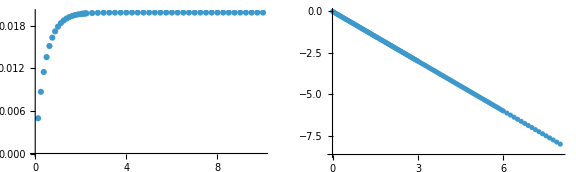

```mathematica
P1=ListPlot[Transpose[{x//Abs,ηarray}],PlotRange->All];
P2=ListPlot[Transpose[{y//Abs,ϵarray}],PlotRange->All,ScalingFunctions->"Log10"];
GraphicsGrid[{{P1,P2}},ImageSize->Large]
```

#### Computation

Options (opt):
	1. True → New values of ϵ are added to an existing file;
	2. True → New values of η are added to an existing file (if 1. is also True it prevails);
	 	- Default (i.e. 1. and 2. are both False) create a new file with user-entered starting guess.
	 3. True → Gives the correct shape output when ϵ is the initialization parameter.

```mathematica
opt={False,False,False};
```

```mathematica
Which[
opt[[1]],in=Import["QNM_ECO1_heoc_53.m"];ωguess=in[[1,-1,3]];(* same ηs and adding ϵs *)
Print["Dim[in]",in//Dimensions],
opt[[2]],in=Import["QNM_ECO1_heoc_34.m"];ωguess=in[[-1,1,3]];(* same ϵs and adding ηs *)
Print["\nDim[in]",in//Dimensions],
True,ωguess=(*2/5-1/10 ⅈ*)0.41029219691343865755656481837481117539`20.-0.01210110293339904243328231521370532767`20. ⅈ;(* default: new run *)];

Print["ω_guess = ",ωguess//N];
```

```mathematica
EQ=EQRW;BC=EcoBC[{},coefInf];
```

```mathematica
new=GridSearchECO[2/5-ⅈ/10,{M->1,l->2,match->10,inf->50,gInf[0]->1},SubsHE,{{{0,0,1}},{{-8,-6-1/8,1/8},{-6,-3-1/16,1/16},{-3,0,1/32}}}];

Print["Dim[new] = ",new//Dimensions];
```

```mathematica
If[opt[[3]],new=new//Transpose]; 
Which[
opt[[1]]||opt[[2]],out=Join[in//Transpose,new//Transpose]//Transpose,
True,out=new];
Print["Dim[out] = ",out//Dimensions];
```

OUTPUT FILE

Data format: N×M matrix with elements {η, ϵ, Re[ω], Im[η], check}, where N=Length[ai] and M=Length[aj]. 
	`ai` is the initialization parameter and `aj` is the parallel parameter (i.e. explored in parallel).
Name format:
	- Object type : ECO1, i.e. non-spinning ECO;
	- Parameters : match_inf_ordI-ordE (if equal one is omitted);
	- Output           : h(=η)_e(=ϵ)_R(=Re[ω])_I(=Im[ω])_c(=check);
	- Two digits code giving information about the integration order as follows:
		· First and second digits refer respectively to η and ϵ;
		· Exploration from lower to higher → +1, vice versa → +0;
		· Parallel parameter +2;
		· Parameter with values added in successive runs +4 (usually the initialization parameter).
	- File numeration (i.e. different run and/or parameter volume).

```mathematica
(* --- Output file --- *)
Export["Data_GSearch\\ECO1_10_50_10_heRIc_-1_1.m",out];Clear[new,out];
```

## Kerr

### Spin

#### Parameters grid

```mathematica
χarray={10^-2,5 10^-2,10^-1,15 10^-2,2 10^-1,25 10^-2,3 10^-1};
ωtrue={0.3749365685-0.08894183057ⅈ,0.3801455748-0.08884890191ⅈ,0.3870175384-0.08870569903ⅈ,0.3943329877-0.08852826817ⅈ,0.4021453242-0.08831116621ⅈ,0.4105179098-0.08804765025ⅈ,0.4195266818-0.08772927189ⅈ};
(*ωguess={};*)
```

#### Computation

```mathematica
(* !! --- To be updated --- !! *)
ωfound=Table[{},{i,χarray}];ωguess=2/5-1/10 ⅈ;
Monitor[Do[ωfound[[i]]={χarray[[i]],ωtrue[[i]],FindQNM[ωguess,χarray[[i]]][[1]]};ωguess=ωfound[[i,-1]],
{i,1,Length[χarray]}],Row["Iteration: i = ",i]];
```

OUTPUT FILE

Data format: N “matrix” with elements {χ, Re[ω], Im[η], check}, where N=Length[χ].
Name format:
	- Object type : Kerr, i.e. spinning BH;
	- Parameters : eps_match_inf_ordI-ordE (if equal one is omitted);
	- Output           : x(=χ)_R(=Re[ω])_I(=Im[ω])_c(=check);
	- File numeration (i.e. different run and/or parameter volume).

```mathematica
(* --- Output file --- *)
Export["Data_GSearch\\",out];Clear[out];
```

QNM_Kerr_generale.dat

```mathematica
(* con ordHor=3
1.403173173208927*^-7-2.594252477838843*^-7 ⅈ,1.3839418633310174*^-7-2.5434630081255793*^-7 ⅈ,1.305543594343206*^-7-2.399207012504512*^-7 ⅈ *)
```

```mathematica
(* con ordHor=7
1.403173173208927*^-7-2.594252477838843*^-7 ⅈ,1.3839418633310174*^-7-2.5434630081255793*^-7 ⅈ,1.305543594343206*^-7-2.399207012504512*^-7 ⅈ *)
```

## Old stuff

```mathematica
GridSearch[par_,steps_]:=Module[{axis,data,i},
axis=Table[Union@@Table[Table[k,{k,j[[1]],j[[2]],j[[3]]}],{j,i}],{i,steps}];i=0;
data=Monitor[Outer[i++;Join[{##},FindQNM[par[[1]],{##},par[[2]]]]&,Sequence@@axis],Row[{"Iteration: i = ",i}]];
Return[data];
];
```

```mathematica
steps={{{1,5,1}},{{1,10,2}}};
axis=Union@@@Map[Range@@#&,steps,{2}];i=0;
data=Monitor[i++;Join[{##},Exp[{##}]]&@@@Tuples[axis],Row[{"Iteration: i = ",i}]];
```

```mathematica
dims=Length/@axis;
Fold[Partition,data,Reverse@Rest@dims]//MatrixForm
```

```mathematica
Output[par_,theta_]:=Module[{data},
data=FindQNM[];
];
```

```mathematica
{ai,aj}=Union@@@Map[Range@@#&,{{{1,5,1}},{{1,10,2}}},{2}];
DistributeDefinitions[RunLine,fun];
par={0,0};
Print[Thread[{First[aj],ai}]];
row1=RunLine[par[[1]],par[[2]],Thread[{First[aj],ai}]];        (*j=1,sequenziale su i*)
cols=ParallelMap[Prepend[RunLine[#[[3]],par[[2]],Thread[{Rest[aj],#[[2]]}]],#]&,row1,Method->"FinestGrained"];
```

{{1,1},{1,2},{1,3},{1,4},{1,5}}

```mathematica
points=Tuples[arrays];
total=Length[points];
count=0;current=None;
SetSharedVariable[count,current];

flat=Monitor[ParallelMap[With[{r=f[p1,p2,#]},count++;current=#;Join[#,r]]&,points,Method->"FinestGrained"],Row[{ProgressIndicator[count,{0,total}],"  ",count,"/",total,"   ultimo punto: ",current}]];

res=Fold[Partition,flat,Reverse@Rest@dims];
```

## Random Search

In this Chapter the hyperparameter space is explored randomly. This approach allows for a relatively fast search over the selected volume.
The implementation is the following:
	- RandomSearch: handles sampling, calculation and final output;
	- See above for IntQNM and FindQNM.

### Functions

```mathematica
(* --- RandomSearch --- *)
(* NOTE: *)
(* par_ = {Subscript[ω, guess], Subscript[ω, true], and list of rules for CO parameters (see IntQNM above)} *)
(* ops_    : functions to set hyperparameters taking as input an uniformly distributed random variable *)
(* ranges_ : ranges of each uniform distribution *)
(* n_      : number of iterations *)
(* output  : {theta, Re[Δω], Im[Δω], Abs[Δω]} where Δω = Subscript[ω, found] - Subscript[ω, true] *)
RandomSearch[par_,ops_,ranges_,n_]:=Module[{data,theta,Δω},
data={};
Monitor[Do[
theta=MapThread[#1[#2]&,{ops,RandomVariate[UniformDistribution[#]]&/@ranges}];
Δω=FindQNM[par[[1]],par[[3]],theta][[1]]-par[[2]];
AppendTo[data,Join[theta,{Re[Δω],Im[Δω],Abs[Δω]}]],{i,n}],Row[{"Iteration: i = ",i}]];
Return[data];
];
```

```mathematica
(* --- RandomSearch V2 --- to be tested *)
(* NOTE: *)
(* par_    : list of rules for CO parameters (see IntQNM above) *)
(* ops_    : list of functions to set hyperparameters taking as input an uniformly distributed random variable *)
(* ranges_ : ranges of each uniform distribution *)
(* n_      : number of iterations *)
(* output  : {theta, Re[ω], Im[ω], check} *)
RandomSearch[ω0_,par_,ops_,ranges_,n_]:=Module[{data,theta,i=0},
theta=MapThread[#1[#2]&,{ops,RandomVariate[UniformDistribution[#],n]&/@ranges}]//Transpose;
data=Monitor[i++;Join[{##},FindQNM[ω0,par,{##}]]&@@@theta,Row[{ProgressIndicator[i,{0,n}]," ",i,"/",n}]];
Return[data];
];
```

## Schwarzschild (eps, match, inf)

```mathematica
FindQNM[ωguess_,par_,theta_]:=Module[{g,ωroot},
g[x_?NumericQ]:=IntQNM[x,Join[{2},theta],coefHor,coefInf][[1]];
ωroot=x/.FindRoot[g[x]==0,{x,ωguess},AccuracyGoal->6,WorkingPrecision->20][[1]];

Return[{ωroot,Abs[g[ωroot]]}];
]
```

```mathematica
EQ=EQRW;BC=SchwBC[Import["SeriesCoef\\CoefHor_Schw_10.m"],Import["SeriesCoef\\CoefInf_Schw_10.m"]];
```

```mathematica
ωSBH=(0.7473433688360838- 0.1779246313778714ⅈ)/2;ωguess=2/5-ⅈ/10;
par={l->2,M->1};
(* --- Output File --- *)
(* Name format: *)
(* parameters    : expansion order (horizon-infinty, if equal one is omitted) *)
(* output format : {ϵ, μ, ι, Re[Δω], Im[Δω], Abs[Δω]} *)
(* file numeration (i.e. different run and different hyperparameters) *)
fileName="Schw_10_emidRdIdA_2.m";
```

```mathematica
data=RandomSearch[{ωguess,ωSBH,par},{10^#&,#&,#&},{{-10,-3},{5,10},{60,60}},500];
Print["Dim[data] = ",data//Dimensions];
```

Dim[data] = {500}

```mathematica
(* --- Output File --- *)
Export["Data_RSearch\\"+fileName,data];Clear[data];
```

### Integration parameters (eps, match, inf)

```mathematica
(* !! --- Updated version from here --- !! *)
EQ=EQRW;BC=SchwBC[Import["SeriesCoef\\CoefHor_Schw_10.m"],Import["SeriesCoef\\CoefInf_Schw_10.m"]];
```

```mathematica
ωguess=2/5-ⅈ/10;par={l->2,M->1};
out=RandomSearch[ωguess,par,{10^#&,#&,#&},{{-10,-3},{5,10},{60,60}},500];

Print["Dim[out] = ",out//Dimensions];
```

OUTPUT FILE

Data format: length N “matrix” with elements {eps, match, inf, Re[ω], Im[η], check}, where N=number of points.
Name format:
	- Object type : Schw, i.e. Schwarzschild BH;
	- Parameters : ordI-ordE (if equal one is omitted);
	- Output           : e(=eps)_m(=match)_i(=inf)_R(=Re[ω])_I(=Im[ω])_c(=check);
	- File numeration (i.e. different run and/or parameter volume).

```mathematica
(* --- Output file --- *)
Export["Data_RSearch\\",out];Clear[out];
```

## Kerr (eps, match, inf)

```mathematica
EQ=EQT;BC=KerrBC[Import["SeriesCoef\\CoefHor_Kerr_4.m"],Import["SeriesCoef\\CoefInf_Kerr_10.m"]];
```

```mathematica
ωSBH=(0.7473433688360838- 0.1779246313778714ⅈ)/2;ωguess=2/5-ⅈ/10;
par={l->2,m->2,s->-2,M->1,χ->0};
(* --- Output File --- *)
(* Name format: *)
(* parameters    : expansion order (horizon-infinty, if equal one is omitted) *)
(* output format : {ϵ, μ, ι, Re[Δω], Im[Δω], Abs[Δω]} *)
(* file numeration (i.e. different run and different hyperparameters) *)
fileName="Kerr_0_4-10_emidRdIdA_1.m";
```

```mathematica
(*{42/100-87/1000 ⅈ,0.4195266818-0.08772927189ⅈ,0.3}*)
data=RandomSearch[{2/5-1/10 ⅈ,ωSBH,0},{10^#&,#&,#&},{{-10,-3},{5,15},{30,130}},FindQNM,1000];
Print["Dim[data] = ",data//Dimensions];
```

```mathematica
(* --- Output file --- *)
(* Name format: *)
(* parameters    : spin (. is omitted)_expansion order (horizon-infinty, if equal one is omitted) *)
(* output format : {ϵ, μ, ι, Re[Δω], Im[Δω], Abs[Δω]} *)
(* file numeration (i.e. different run and different hyperparameters) *)
Export["Data_RSearch\\Kerr_0_4-10_emidRdIdA_1.m",data];Clear[data];
```

### Integration parameters (eps, match, inf)

```mathematica
(* !! --- Updated version from here --- !! *)
EQ=EQT;BC=KerrBC[Import["SeriesCoef\\CoefHor_Kerr_4.m"],Import["SeriesCoef\\CoefInf_Kerr_10.m"]];
```

```mathematica
ωguess=2/5-ⅈ/10;par={l->2,m->2,s->-2,M->1,χ->0};(*{42/100-87/1000 ⅈ,0.4195266818-0.08772927189ⅈ,0.3}*)
out=RandomSearch[ωguess,par,{10^#&,#&,#&},{{-10,-3},{5,15},{30,130}},FindQNM,1000];
Print["Dim[out] = ",out//Dimensions];
```

OUTPUT FILE

Data format: length N “matrix” with elements {eps, match, inf, Re[ω], Im[η], check}, where N=number of points.
Name format:
	- Object type : Kerr, i.e. Kerr BH;
	- Parameters : χ (. is omitted)_ordI-ordE (if equal one is omitted);
	- Output           : e(=eps)_m(=match)_i(=inf)_R(=Re[ω])_I(=Im[ω])_c(=check);
	- File numeration (i.e. different run and/or parameter volume).

```mathematica
(* --- Output file --- *)
Export["Data_RSearch\\Kerr_0_4-10_emidRdIdA_1.m",out];Clear[out];
```

## ECO - Stationary

### Integration parameters (match, inf)

```mathematica
EQ=EQRW;BC=EcoBC[{},Import["SeriesCoef\\CoefInf_Schw_10.m"]];
```

```mathematica
ωguess=2/5-ⅈ/10;par={l->2,M->1,η->1/(16π),ϵ->10^-10};
out=RandomSearch[ωguess,par,{#&,#&},{{5,15},{50,150}},1000];
Print["Dim[out] = ",out//Dimensions];(* data=Sort[data,#1[[-1]]<#2[[-1]]&]; *)
```

OUTPUT FILE

Data format: length N “matrix” with elements {match, inf, Re[ω], Im[η], check}, where N=number of points.
Name format:
	- Object type : ECO1, i.e. non-spinning ECO;
	- Parameters : log[η']_log[ϵ]_ordI-ordE (if equal one is omitted);
	- Output           : e(=eps)_m(=match)_i(=inf)_R(=Re[ω])_I(=Im[ω])_c(=check);
	- File numeration (i.e. different run and/or parameter volume).

```mathematica
(* --- Output file --- *)
Export["Data_RSearch\\",out];Clear[out];
```

## Old stuff

```mathematica
data={};n=250;
Module[{ϵ,μ,ι,ωfound,check},Monitor[Do[
ϵ=10^-7(*RandomVariate[UniformDistribution[{-7,-3}]]*);μ=RandomVariate[UniformDistribution[{5,15}]];ι=60(*RandomVariate[UniformDistribution[{25,150}]]*);
ωfound=FindQNM[ωguess,{2,ϵ,μ,ι}][[1]];
AppendTo[data,{ϵ,μ,ι,ωfound,Abs[ωfound-ωSBH]}],
{i,n}],Row[{"Iteration: i = ",i}]]];
data=Sort[data,#1[[-1]]<#2[[-1]]&];
Print["Dim[data] = ",data//Dimensions];
```